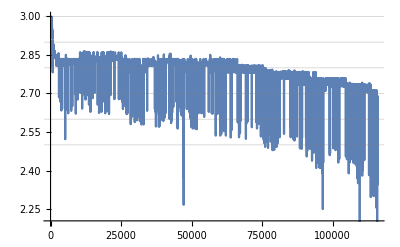

```mathematica
ListLinePlot[
MovingAverage[
Import["!ssh nas 'cat /tmp/battery1.log | grep voltage'","Table"][[;;,6]],
1
],
PlotRange->{2.2,3.0},
GridLines->{{},{2.0,2.5,2.6,2.7,2.8,2.9,3.0}}
]
```

```mathematica
time=Import["/Users/jiahao/Desktop/scope_0.csv", "Data"][[3;;,1]];
voltages=Import["/Users/jiahao/Desktop/scope_0.csv", "Data"][[3;;,2]];
smooth=10;
ListLinePlot[Transpose[{time[[smooth;;]], MovingAverage[voltages+0.00207935,smooth]}],AxesOrigin->{0,0}]
```